# How Strong are Giants?

Elan Rotenberg

If you were twice your size, would you be twice as “strong”? More precisely, if your volume doubled, everything proportionally, could you still lift twice your weight?

It does not mater what shape your are, your volume is always proportional to the cube of your length:

```mathematica
Volume[Ball[{0,0,0},r]]
```

(4 π r^3)/3

```mathematica
Volume[Cuboid[{0,0,0},{r,r,r}]]
```

Abs[r]^3

And the surface area is always proportional to the square of your length.

```mathematica
SurfaceArea[Ball[{0,0,0},r]]
```

4 π r^2

```mathematica
SurfaceArea[Cuboid[{0,0,0},{r,r,r}]]
```

6 Abs[r]^2

Also, the force that a muscle can exert is proportional to the surface of its cross-section, which is in turn proportional to your surface. Therefore if your volume doubles, the force that your muscle can exert would change by a factor:

```mathematica
SurfaceRatio=Power[2,2/3.]
```

1.5874

Let’s say that your weight is 200 "lb" and you can lift 400 "lb":

```mathematica
Weight=Quantity[200, "Pounds"]
```

200 lb

```mathematica
Lift=Quantity[400, "Pounds"]
```

400 lb

Then if your weight were to double:

```mathematica
NewWeight=Quantity[400, "Pounds"]
```

400 lb

You would be able to li.08ft:

```mathematica
Lift*SurfaceRatio
```

634.96 lb

Not double your weight anymore, but still impressive.

But what about some of the giants in Game of Thrones?
If we find the height, then we can find the scale factor of a regular person to the giants.
Let us assume an average man is

```mathematica
Height=LinguisticAssistant
```

5 10

```mathematica
Weight
```

200 lb

```mathematica
img=-Graphics-
```

-Graphics-

In order to find the scale factor, find the height of Mag and the height of the Soldier

```mathematica
MagTheMighty=-Graphics-;
```

```mathematica
Soldier=-Graphics-;
```

```mathematica
ScaleFactor=ImageDimensions[MagTheMighty]⟦2⟧/ImageDimensions[Soldier]⟦2⟧//N
```

3.48529

Therefore his height would be:

```mathematica
GiantHeight=ScaleFactor*Height
```

20 3.97059

And his weight would be proportional to the cube of his length:

```mathematica
GiantWeight=Power[ScaleFactor,3]*Weight
```

8467.37 lb

And he would be able to lift:

```mathematica
Lift*Power[GiantWeight/Weight,2/3]//N
```

4858.91 lb

While this is an impressive feat, the giant can only lift about half his bodyweight.

Let us look at data to see if our result supports our hypothesis.

```mathematica
Records=Import[];
```

```mathematica
Sample=RandomSample[Records,500000];
```

```mathematica
MaleSample=Select[Sample,];
```

```mathematica
Data=Table[2.2*MaleSample[[n]][[{8,25}]],{n,Length[MaleSample]}];
```

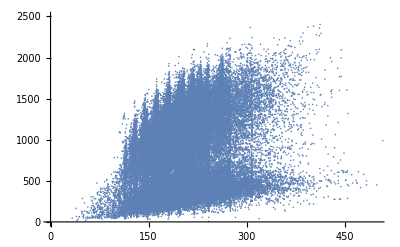

```mathematica
PlotDataAll=ListPlot[Data,PlotRange->{{0,500},{0,2500}}]
```

It seems like we have 2 basic structures with similar patterns. This is most likely due to two main groups of people who are lifting: one with more average strength, the other with greater strength.
Let’s isolate each pattern and find a curve that fits nicely

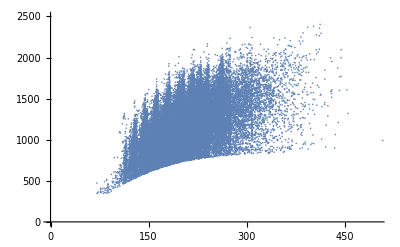

```mathematica
MaleSampleStrong=Select[Sample,];
DataStrong=Table[2.2*MaleSampleStrong[[n]][[{8,25}]],{n,Length[MaleSampleStrong]}];
PlotDataStrong=ListPlot[DataStrong,PlotRange->{{0,500},{0,2500}}]
```

```mathematica
FitDataStrong=Fit[DataStrong,{1,x^(2/3)},x]
```

194.447+28.9701 x^(2/3)

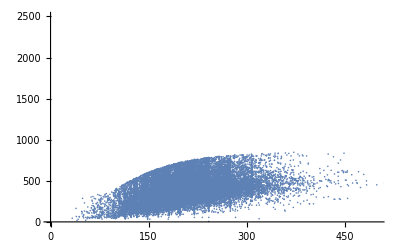

```mathematica
MaleSampleAvg=Select[Sample,];
DataAvg=Table[2.2*MaleSampleAvg[[n]][[{8,25}]],{n,Length[MaleSampleAvg]}];
PlotDataAvg=ListPlot[DataAvg,PlotRange->{{0,500},{0,2500}}]
```

```mathematica
FitDataAvg=Fit[DataAvg,{1,x^(2/3)},x]
```

-12.9609+11.3905 x^(2/3)

Let us see if these “fits” are a good approximation of our data set

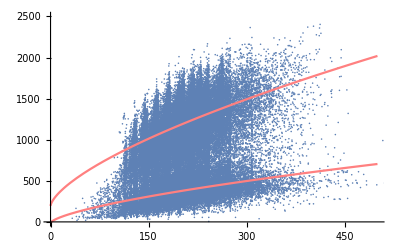

```mathematica
Show[PlotDataAll,Plot[FitDataStrong,{x,0,500},PlotStyle->Pink],Plot[FitDataAvg,{x,0,500},PlotStyle->Pink]]
```

This is a good fit!
This is an application of Galileo’s Square Cube Law, which states
“When an object undergoes a proportional increase in size, its new surface area is proportional to the square of the multiplier and its new volume is proportional to the cube of the multiplier.”
This explains why the model of

```mathematica
F(x)=a+bx^(2/3)
```

fits the data very well.

We can extend this by giving a plot example (with coefficient 1 for simplicity) that estimates how strong a 200 pound person would be if their weight doubled, quadrupled etc. (with everything else growing proportionally) and they were originally lifting either 1XBodyweight, 2XBodyweight, 3XBodyweight, or 4XBodyweight.

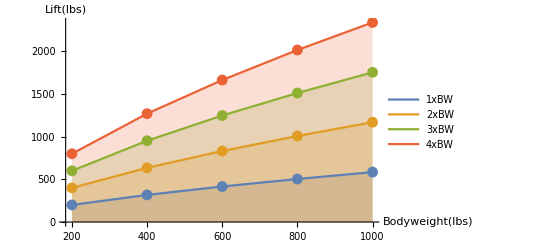

```mathematica
StrengthLevel[lift_,bodyweight_]:=(#1 bodyweight->lift #1^(2/3)&)/@Range[1,5]
AllStrengthData=StrengthLevel[#,200]&/@Range[200,800,200];
ListLinePlot[Table[Table[{Keys[AllStrengthData⟦m⟧⟦n⟧],Values[AllStrengthData⟦m⟧⟦n⟧]},{n,Length[AllStrengthData⟦m⟧]}],{m,Length[AllStrengthData]}],Mesh->All,Filling->Axis,PlotLegends->{"1xBW","2xBW","3xBW","4xBW"},AxesLabel->{"Bodyweight(lbs)","Lift(lbs)"}]
```

This analysis works well with people because we share similar structures. Nevertheless, there is a point at which a person gets so large that they can not even support their own weight. This giant would be very unlikely to be able to live as he can only manage to lift, at most, half of his bodyweight. There is a reason why there has never been a person that giant.